```mathematica
(* Closed, kappa > 0, 4 real roots: 2 kt^3/mt^2 > gp(x) > gm(x) *)
(* In this case, there is a contour satisfying Witten's criterion. *)

Clear[lam,k,m,r,kt,mt,rt,f,Pp,Qq,xh,z0,e0,app,apm,amp,amm]

lam=1.;
k=1.;
m=.5; (* set matter to be zero for simplication*)
x=1;
r=(x m^2)/k;
gp[x]=((1+8 x)+(1+8/3 x)√(1+32/3 x))/(1+3 √(1+32/3 x));
gm[x]=((1+8 x)-(1+8/3 x)√(1+32/3 x))/(1-3 √(1+32/3 x));
kt=k/lam;
mt=m/lam;
rt=r/lam;
(2 kt^3)/mt^2-gp[x]
(2 kt^3)/mt^2-gm[x]
f=a^4-3 kt a^2+mt a+rt;
V=-lam f;
Pp=-4/3 rt-kt^2;
Qq=-mt^2/2+kt^3-4 kt rt;
xh=(-Qq+√(Qq^2+Pp^3))^(1/3);
z0=2 kt+xh-Pp/xh;
e0=z0^(1/2);
app=1/2((+e0)+√(-(+e0)^2-2mt/(+e0)+6 kt));
apm=1/2((+e0)-√(-(+e0)^2-2mt/(+e0)+6 kt));
amp=1/2((-e0)+√(-(-e0)^2-2mt/(-e0)+6 kt));
amm=1/2((-e0)-√(-(-e0)^2-2mt/(-e0)+6 kt));
app+apm+amp+amm

Solve[V==0,a]
{app,apm,amp,amm}

a1=app;
a2=apm;
a3=amp;
a4=amm;

mm=((a2-a3)(a1-a4))/((a1-a3)(a2-a4));
rho=1/2 √(lam/3(a1-a3)(a2-a4));
a[eta_]:=(a2(a3-a1)-a1(a3-a2)JacobiSN[rho eta,mm]^2)/((a3-a1)-(a3-a2)JacobiSN[rho eta,mm]^2);
(*ContourPlot[Re[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]
ContourPlot[Im[a[x+ⅈ*y]],{x,-10,10},{y,-10,10}]*)
```

6.08623

7.6189

0.+0. ⅈ

{{a→-1.78923},{a→-0.218388},{a→0.397315},{a→1.61031}}

{1.61031+0. ⅈ,0.397315+0. ⅈ,-0.218388+0. ⅈ,-1.78923+0. ⅈ}

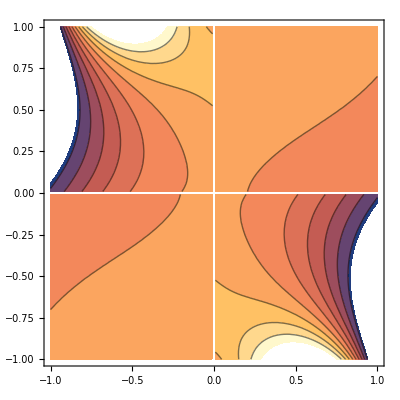

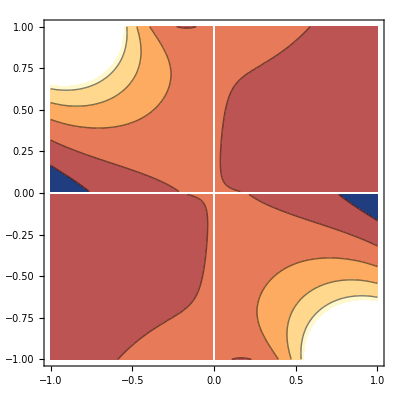

```mathematica
Clear[ks,kc,alpha,gamma,fun,heun,Phia,Phieta]
ks=10;
kc=3/2 kt;
alpha=I*kc+(1-kc^2)^(1/2);
gamma=alpha*(alpha-1)/(2*alpha^2+2);
fun[a_]:=Exp[-1/2*(1-I*kc)*ArcTan[(-I*kc+I*a^2)/(kc^2-1)^0.5]/(kc^2-1)^0.5]*Exp[I/4*ArcTan[2*kc*I*a^2/(a^4+1)]]*(1+(2-4*kc^2)*a^4+a^8)^(1/8);
heun[a_]:=(I*a^2/alpha-1)^(-gamma)*(alpha*I*a^2+1)^gamma*HeunG[-1/alpha^2,(5*alpha-ks^2*I)/(4*alpha),1,5/2,5/2,1/2,a^2*I/alpha];
Phia[a_]:=fun[a]*heun[a];
Phieta[eta_]:=Phia[a[eta]];
ContourPlot[Re[Phieta[x+ⅈ*y]],{x,-1,1},{y,-1,1}]
ContourPlot[Im[Phieta[x+ⅈ*y]],{x,-1,1},{y,-1,1}]
```

```mathematica
$Assumptions={r>0,m>0,κ>0,κ<1,k>0};
FullSimplify[DSolve[{(r+m a-2κ a^2+a^4)Phi''[a]+(4r/a+4 m-10 κ a +6 a^3)Phi'[a]+a(4 a^2+k^2-8κ)Phi[a]==0,Phi[0]==1,Phi'[0]==0},Phi[a],a]]
```

DSolve[{a (4 a^2+k^2-8 κ) Phi[a]+(6 a^3+4 m+(4 r)/a-10 a κ) Phi'[a]+(r+a (a^3+m-2 a κ)) Phi''[a]==0,Phi[0]==1,Phi'[0]==0},Phi[a],a]